## Input Data

```mathematica
Off[ClebschGordan::tri];
Off[ClebschGordan::phy];
Off[SixJSymbol::tri];
Off[SixJSymbol::phy];
ParallelEvaluate[Off[ClebschGordan::tri]];
ParallelEvaluate[Off[SixJSymbol::tri]];
ParallelEvaluate[Off[Infinity::indet]];
ParallelEvaluate[Off[ClebschGordan::phy]];
ParallelEvaluate[Off[ClebschGordan::tri]];
ParallelEvaluate[Off[NIntegrate::eincr]];
ParallelEvaluate[Off[NIntegrate::slwcon]];
SetDirectory[StringJoin[NotebookDirectory[]]]
```

/Users/zhan/bsmllh/nb/theDD

```mathematica
m={1.,4.,4.};
fileName="be/be3";
importedData=Import[FileNameJoin[{NotebookDirectory[], StringJoin[fileName,".wf"]}], "Table"];
γ={};
dataList={};
tempList={};
AppendTo[γ,importedData⟦1⟧];
Do[
If[IntegerQ@importedData⟦i,1⟧,
AppendTo[γ,importedData⟦i⟧];
AppendTo[dataList,tempList];
tempList={};
,
AppendTo[tempList,importedData⟦i⟧];
];
,{i,2,Length@importedData}];
AppendTo[dataList,tempList];
Clear[tempList];
```

```mathematica
Cij={};
αij={};
βij={};
Do[
tempCij={};
tempαij={};
tempβij={};
Do[
If[i==j,AppendTo[tempCij,dataList⟦k,i,3⟧dataList⟦k,j,3⟧]
,AppendTo[tempCij,2dataList⟦k,i,3⟧dataList⟦k,j,3⟧]];
AppendTo[tempαij,2(dataList⟦k,i,1⟧+dataList⟦k,j,1⟧)];
AppendTo[tempβij,2(dataList⟦k,i,2⟧+dataList⟦k,j,2⟧)];
,{i,1,Length@dataList⟦k,All,3⟧},{j,1,i}];
AppendTo[Cij,tempCij];
AppendTo[αij,tempαij];
AppendTo[βij,tempβij];
,{k,1,Length@γ}];
```

```mathematica
(*T=Module[{c,s},
c=-√((m⟦1⟧m⟦2⟧)/((m⟦1⟧+m⟦3⟧)(m⟦2⟧+m⟦3⟧)));
s=(-1)^(2-1)Sign[1-2] √(1-c^2);
{{c,s},{-s,c}}];*)
(*T={{-√((m⟦1⟧m⟦2⟧)/((m⟦1⟧+m⟦3⟧)(m⟦2⟧+m⟦3⟧))),-√((m⟦3⟧(m⟦1⟧+m⟦2⟧+m⟦3⟧))/((m⟦1⟧+m⟦3⟧)(m⟦2⟧+m⟦3⟧)))},{√((m⟦3⟧(m⟦1⟧+m⟦2⟧+m⟦3⟧))/((m⟦1⟧+m⟦3⟧)(m⟦2⟧+m⟦3⟧))),-√((m⟦1⟧m⟦2⟧)/((m⟦1⟧+m⟦3⟧)(m⟦2⟧+m⟦3⟧)))}};*)
(*T={{-m⟦2⟧/(m⟦2⟧+m⟦3⟧),1},{-(m⟦3⟧(m⟦1⟧+m⟦2⟧+m⟦3⟧))/((m⟦2⟧+m⟦3⟧)(m⟦1⟧+m⟦3⟧)),-m⟦1⟧/(m⟦1⟧+m⟦3⟧)}};*)
T={{-√((m⟦1⟧m⟦2⟧)/((m⟦1⟧+m⟦3⟧)(m⟦2⟧+m⟦3⟧))),-√((m⟦3⟧(m⟦1⟧+m⟦2⟧+m⟦3⟧))/((m⟦1⟧+m⟦3⟧)(m⟦2⟧+m⟦3⟧)))},{√((m⟦3⟧(m⟦1⟧+m⟦2⟧+m⟦3⟧))/((m⟦1⟧+m⟦3⟧)(m⟦2⟧+m⟦3⟧))),-√((m⟦1⟧m⟦2⟧)/((m⟦1⟧+m⟦3⟧)(m⟦2⟧+m⟦3⟧)))}};
Q=T.{{1,p},{0,1}};
Protect[p];
Det[T]
μij=T⟦1,1⟧^2 αij+T⟦2,1⟧^2 βij;
νij=T⟦1,2⟧^2 αij+T⟦2,2⟧^2 βij;
ρij=(T⟦1,1⟧T⟦1,2⟧αij+T⟦2,1⟧T⟦2,2⟧βij);
ωij=νij-ρij^2/μij;
```

1.

## Independence of the y angular variables in Exp

```mathematica
𝒾[l_,x_]:=√(Pi/(2 x))BesselI[l+1/2,x];
With[{x={0.91,xTh,xPh},y={0.5,0.5,0.516}},
{4Pi 𝒾[0,x⟦1⟧ y⟦1⟧],
NIntegrate[Sin[xTh]Exp[FromSphericalCoordinates[x].FromSphericalCoordinates[y]],{xTh,0,Pi},{xPh,0,2Pi}]}]
```

{13.0045,13.0045}

## an Eq. from the Varga Suzuki book

```mathematica
ℐ[n_,l_,ν_,ω_]:=√(Pi/2)((2n)!!ω^l)/ν^(n+l+3/2)Exp[ω^2/(2ν)]LaguerreL[n,l+1/2,-ω^2/(2ν)];
ℐ[n_,a_]:=Gamma[1/2+n/2]/(2 a^(1/2+n/2));
With[{n=3,l=0,ν=1.2,ω=0.654},
Print[ℐ[n,l,ν,ω]];
Print[NIntegrate[y^(2n+l+2)Exp[-1/2 ν y^2]𝒾[l,ω y],{y,0,Infinity}]];
]
```

95.7027

95.7027

## Normalization of each partial wave and the total wave function

```mathematica
Total[Cij⟦#⟧ℐ[2+2γ⟦#,1⟧,1/2 αij⟦#⟧]ℐ[2+2γ⟦#,2⟧,1/2 βij⟦#⟧]]&/@Range[1,Length@Cij];
𝒩=%
Total@%
```

{0.997769340407512,0.0022306595922731705}

0.999999999999786

```mathematica
γForCalc=Flatten[Position[𝒩,_?(#>0.1&)]]
```

{1}

## Some needed formulas

```mathematica
𝒴[j1_,j2_,j_,x_,y_]:=Sum[ClebschGordan[{j1,jm1},{j2,jm2},{j,j}]
SphericalHarmonicY[j1,jm1,x⟦2⟧,x⟦3⟧]SphericalHarmonicY[j2,jm2,y⟦2⟧,y⟦3⟧],{jm1,-j1,j1},{jm2,-j2,j2}];
uNineJ[{{a_, b_, c_}, {d_, e_, f_}, {g_, h_, j_}}]:=Total[√((2c+1)(2f+1)(2g+1)(2h+1))(-1)^(2#)(2#+1)SixJSymbol[{a,b,c},{f,j,#}]SixJSymbol[{d,e,f},{b,#,h}]SixJSymbol[{g,h,j},{#,a,d}]&/@Range[0,4]];
ℭ[l1_,l2_,L_]:=√(((2l1+1)(2l2+1))/(4Pi (2L+1)))ClebschGordan[{l1,0},{l2,0},{L,0}];
𝔇[l1_,l2_,L_]:=√((4Pi (2L+1)!)/((2l1+1)!(2l2+1)!));
𝔈[{{a_, b_, c_}, {d_, e_, f_}, {g_, h_, j_}}]:=uNineJ[{{a, b, c}, {d, e, f}, {g, h, j}}]ℭ[a,d,g]ℭ[b,e,h];
triQ[a_,b_,c_]:=If[Abs[a-b]≤c≤a+b&&Abs[a-c]≤b≤a+c&&Abs[b-c]≤a≤b+c,True,False];
```

```mathematica
𝒴2ij[k_,x_,y_]:=Block[{λ=γ⟦k,1⟧,l=γ⟦k,2⟧,L=γ⟦k,3⟧,sum=0.0,j91,j92,dataList={},inc},
Do[
If[!triQ[λ1i,λ-λ1i,λ],Continue[]];
If[!triQ[l1i,l-l1i,l],Continue[]];
If[!triQ[λ-λ1i,l-l1i,ℓ2],Continue[]];
If[!triQ[λ1i,l1i,ℓ1],Continue[]];
If[!triQ[λ,l,L],Continue[]];
If[!triQ[ℓ1,ℓ2,L],Continue[]];
If[!triQ[λ1j,λ-λ1j,λ],Continue[]];
If[!triQ[l1j,l-l1j,l],Continue[]];
If[!triQ[λ-λ1j,l-l1j,ℓ2],Continue[]];
If[!triQ[λ1j,l1j,ℓ1],Continue[]];
inc=𝔈[{{λ1i, λ-λ1i, λ}, {l1i, l-l1i, l}, {ℓ1, ℓ2, L}}]𝔈[{{λ1j, λ-λ1j, λ}, {l1j, l-l1j, l}, {ℓ1, ℓ2, L}}] 
𝔇[λ1i,λ-λ1i,λ]𝔇[l1i,l-l1i,l]𝔇[λ1j,λ-λ1j,λ]𝔇[l1j,l-l1j,l] 
Q⟦1,1⟧^(λ1i+λ1j)Q⟦2,1⟧^(l1i+l1j)( Q⟦1,2⟧^(2λ-λ1i-λ1j)Q⟦2,2⟧^(2l-l1i-l1j) /.{p->-ρij⟦k⟧/μij⟦k⟧})
x⟦1⟧^(λ1i+l1i+λ1j+l1j)y⟦1⟧^(2λ+2l-λ1i-l1i-λ1j-l1j)Exp[-1/2(μij⟦k⟧)(x⟦1⟧)^2-1/2(ωij⟦k⟧)(y⟦1⟧)^2];
(*AppendTo[dataList,𝔈[{{λ1i, λ-λ1i, λ}, {l1i, l-l1i, l}, {ℓ1, ℓ2, L}}]];*)
(*Print[{{λ1i, λ-λ1i, λ}, {l1i, l-l1i, l}, {ℓ1, ℓ2, L}},"\t",{{λ1j, λ-λ1j, λ}, {l1j, l-l1j, l}, {ℓ1, ℓ2, L}}];*)
sum+=inc;
,{λ1i,0,λ},{l1i,0,l},{λ1j,0,λ},{l1j,0,l},{ℓ1,0,l+λ},{ℓ2,0,l+λ-ℓ1}];
sum
];
```

```mathematica
W2[k_,x_,y_]:=Total[Cij⟦k⟧ x^2 y^2 𝒴2ij[k,{x,1,1},{y,1,1}]];
```

```mathematica
Hold@NIntegrate[W2[2,x,y],{x,0,Infinity},{y,0,Infinity}]
```

Hold[NIntegrate[W2[2,x,y],{x,0,∞},{y,0,∞}]]

## checking the DD function

```mathematica
Hold@Block[{aij=0.456,Cij=1.39 10^-3,bij=0.341,λ=2,l=1,
y={yr,yTh,yPh},R={3.45,rTh,rPh},ρ0=0.4229 ,γ0=0.7024,ρα,ϕ,
E1,E2},
ρα[r_]:=ρ0 Exp[- γ0 r.r];
ϕ[r_]:=Cij r⟦1⟧^(2l)Exp[-1/2 bij r.r];
E1=ℐ[2+2λ,aij]NIntegrate[
yr^2 Sin[yTh]Sin[rTh]
ρα[FromSphericalCoordinates[R]-FromSphericalCoordinates[y]]
ϕ[{y⟦1⟧,0,0}]
,{yr,0,Infinity},{yTh,0,Pi},{yPh,0,2Pi},{rTh,0,Pi},{rPh,0,2Pi}];
E2=(4Pi)^2 Cij ρ0 Exp[-γ0 R⟦1⟧^2] ℐ[2+2λ,aij]ℐ[l,0,bij+2γ0,2γ0 R⟦1⟧];
{E1,E2}
]
```

Hold[Block[{aij=0.456,Cij=1.39/10^3,bij=0.341,λ=2,l=1,y={yr,yTh,yPh},R={3.45,rTh,rPh},ρ0=0.4229,γ0=0.7024,ρα,ϕ,E1,E2},ρα[r_]:=ρ0 Exp[-γ0 r.r];ϕ[r_]:=Cij r⟦1⟧^(2 l) Exp[-1/2 bij r.r];E1=ℐ[2+2 λ,aij] NIntegrate[yr^2 Sin[yTh] Sin[rTh] ρα[FromSphericalCoordinates[R]-FromSphericalCoordinates[y]] ϕ[{y⟦1⟧,0,0}],{yr,0,∞},{yTh,0,π},{yPh,0,2 π},{rTh,0,π},{rPh,0,2 π}];E2=(4 π)^2 Cij ρ0 Exp[-γ0 R⟦1⟧^2] ℐ[2+2 λ,aij] ℐ[l,0,bij+2 γ0,2 γ0 R⟦1⟧];{E1,E2}]]

## the DDNM of the first cluster

```mathematica
rMax=8.0;
```

```mathematica
ρ1α[k_,R_]:=With[{ρ0=0.4229 ,γ0=0.641(*0.7024*),λ=γ⟦k,1⟧,l=γ⟦k,2⟧,y0=((m⟦2⟧+m⟦3⟧)/(m⟦1⟧+m⟦2⟧+m⟦3⟧))^-1},
(4Pi)^2 Total[Cij⟦k⟧ ρ0 Exp[-γ0 R^2] ℐ[2+2λ,1/2 αij⟦k⟧]ℐ[l,0,(βij⟦k⟧+2γ0)y0^2,2γ0 R]]];
ρ1n[k_,R_]:=With[{λ=γ⟦k,1⟧,l=γ⟦k,2⟧,y0=((m⟦2⟧+m⟦3⟧)/(m⟦1⟧+m⟦2⟧+m⟦3⟧))^-1},
Total[Cij⟦k⟧  R^(2+2l)ℐ[2+2λ,1/2 βij⟦k⟧]Exp[-1/2 βij⟦k⟧(y0 R)^2]]];


Block[{iFunction,data},
data=If[m⟦1⟧==1.,
Table[{R,Total[ρ1n[#,R]&/@γForCalc]},{R,10^-5,rMax,0.1}],
If[m⟦1⟧==4.,Table[{R,Total[ρ1α[#,R]&/@γForCalc]},{R,10^-5,rMax,0.1}]]
];
ρ1=Interpolation[data];
];
```

```mathematica
𝒩1=m⟦1⟧(4Pi NIntegrate[ρ1[r] r^2,{r,10^-5,rMax}])^-1;
```

## the DDNM for the second cluster

```mathematica
ρ2n[k_,y_]:=Block[{λ=γ⟦k,1⟧,l=γ⟦k,2⟧,L=γ⟦k,3⟧,sum=0.0,j91,j92,dataList={},inc,y0=((m⟦1⟧+m⟦3⟧)/(m⟦1⟧+m⟦2⟧+m⟦3⟧))^-1},
Do[
If[!triQ[λ1i,λ-λ1i,λ],Continue[]];
If[!triQ[l1i,l-l1i,l],Continue[]];
If[!triQ[λ-λ1i,l-l1i,ℓ2],Continue[]];
If[!triQ[λ1i,l1i,ℓ1],Continue[]];
If[!triQ[λ,l,L],Continue[]];
If[!triQ[ℓ1,ℓ2,L],Continue[]];
If[!triQ[λ1j,λ-λ1j,λ],Continue[]];
If[!triQ[l1j,l-l1j,l],Continue[]];
If[!triQ[λ-λ1j,l-l1j,ℓ2],Continue[]];
If[!triQ[λ1j,l1j,ℓ1],Continue[]];
inc=𝔈[{{λ1i, λ-λ1i, λ}, {l1i, l-l1i, l}, {ℓ1, ℓ2, L}}]𝔈[{{λ1j, λ-λ1j, λ}, {l1j, l-l1j, l}, {ℓ1, ℓ2, L}}] 
𝔇[λ1i,λ-λ1i,λ]𝔇[l1i,l-l1i,l]𝔇[λ1j,λ-λ1j,λ]𝔇[l1j,l-l1j,l] 
Q⟦1,1⟧^(λ1i+λ1j)Q⟦2,1⟧^(l1i+l1j)( Q⟦1,2⟧^(2λ-λ1i-λ1j)Q⟦2,2⟧^(2l-l1i-l1j) /.{p->-ρij⟦k⟧/μij⟦k⟧})
y^(2λ+2l-λ1i-l1i-λ1j-l1j+2)Exp[-1/2(ωij⟦k⟧)(y0 y)^2]ℐ[λ1i+l1i+λ1j+l1j+2,1/2(μij⟦k⟧)];
(*AppendTo[dataList,𝔈[{{λ1i, λ-λ1i, λ}, {l1i, l-l1i, l}, {ℓ1, ℓ2, L}}]];*)
(*Print[{{λ1i, λ-λ1i, λ}, {l1i, l-l1i, l}, {ℓ1, ℓ2, L}},"\t",{{λ1j, λ-λ1j, λ}, {l1j, l-l1j, l}, {ℓ1, ℓ2, L}}];*)
sum+=inc;
,{λ1i,0,λ},{l1i,0,l},{λ1j,0,λ},{l1j,0,l},{ℓ1,0,l+λ},{ℓ2,0,l+λ-ℓ1}];
Total[Cij⟦k⟧sum]
];

ρ2α[k_,R_]:=Block[{λ=γ⟦k,1⟧,l=γ⟦k,2⟧,L=γ⟦k,3⟧,sum=0.0,j91,j92,dataList={},inc,y0=((m⟦1⟧+m⟦3⟧)/(m⟦1⟧+m⟦2⟧+m⟦3⟧))^-1,ρ0=0.4229 ,γ0=0.641(*0.7024*)},
Do[
If[!triQ[λ1i,λ-λ1i,λ],Continue[]];
If[!triQ[l1i,l-l1i,l],Continue[]];
If[!triQ[λ-λ1i,l-l1i,ℓ2],Continue[]];
If[!triQ[λ1i,l1i,ℓ1],Continue[]];
If[!triQ[λ,l,L],Continue[]];
If[!triQ[ℓ1,ℓ2,L],Continue[]];
If[!triQ[λ1j,λ-λ1j,λ],Continue[]];
If[!triQ[l1j,l-l1j,l],Continue[]];
If[!triQ[λ-λ1j,l-l1j,ℓ2],Continue[]];
If[!triQ[λ1j,l1j,ℓ1],Continue[]];
inc=𝔈[{{λ1i, λ-λ1i, λ}, {l1i, l-l1i, l}, {ℓ1, ℓ2, L}}]𝔈[{{λ1j, λ-λ1j, λ}, {l1j, l-l1j, l}, {ℓ1, ℓ2, L}}] 
𝔇[λ1i,λ-λ1i,λ]𝔇[l1i,l-l1i,l]𝔇[λ1j,λ-λ1j,λ]𝔇[l1j,l-l1j,l] 
Q⟦1,1⟧^(λ1i+λ1j)Q⟦2,1⟧^(l1i+l1j)( Q⟦1,2⟧^(2λ-λ1i-λ1j)Q⟦2,2⟧^(2l-l1i-l1j) /.{p->-ρij⟦k⟧/μij⟦k⟧})
ℐ[(2λ+2l-λ1i-l1i-λ1j-l1j)/2,0,(ωij⟦k⟧+2γ0)y0^2,2γ0 R]ℐ[λ1i+l1i+λ1j+l1j+2,1/2(μij⟦k⟧)];
(*AppendTo[dataList,𝔈[{{λ1i, λ-λ1i, λ}, {l1i, l-l1i, l}, {ℓ1, ℓ2, L}}]];*)
(*Print[{{λ1i, λ-λ1i, λ}, {l1i, l-l1i, l}, {ℓ1, ℓ2, L}},"\t",{{λ1j, λ-λ1j, λ}, {l1j, l-l1j, l}, {ℓ1, ℓ2, L}}];*)
sum+=inc;
,{λ1i,0,λ},{l1i,0,l},{λ1j,0,λ},{l1j,0,l},{ℓ1,0,l+λ},{ℓ2,0,l+λ-ℓ1}];
ρ0 Exp[-γ0 R^2]Total[Cij⟦k⟧sum]
];
```

```mathematica
Block[{iFunction,data},
data=If[m⟦2⟧==1.,
ParallelTable[{R,Total[ρ2n[#,R]&/@γForCalc]},{R,10^-5,rMax,0.1}],
If[m⟦2⟧==4.,ParallelTable[{R,Total[ρ2α[#,R]&/@γForCalc]},{R,10^-5,rMax,0.1}]]
];
ρ2=Interpolation[data];
];
```

```mathematica
𝒩2=2m⟦2⟧(4Pi NIntegrate[ρ2[r] r^2,{r,10^-5,rMax}])^-1;
```

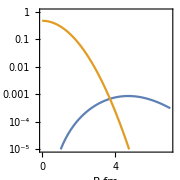

```mathematica
graph1=LogPlot[{𝒩1 ρ1[r],𝒩2 ρ2[r]},{r,10^-5,7},Frame->True,AspectRatio->1,PlotRange->{Automatic,{10^-5,1}},ImageSize->Small,FrameLabel->{"R,fm","ρ(R),fm^-3"}]
```

```mathematica
Export[StringJoin[fileName,"_theDD",".jpg"],graph1,"jpg",ImageResolution->1000];
```

```mathematica
rms=NumberForm[(NIntegrate[( 𝒩1 ρ1[r]+𝒩2 ρ2[r])r^4,{r,10^-5,rMax}]/NIntegrate[(𝒩1 ρ1[r]+𝒩2 ρ2[r])r^2,{r,10^-5,rMax}])^(1/2),{3,2}]
```

2.53

```mathematica
StringRiffle[γ⟦#⟧]&/@Range[Length@γ];
Transpose[{%,NumberForm[#,{4,3}]&/@𝒩}] ;
StringJoin["<(R^2)_m>^(1/2) = ",ToString[rms],"\n",StringRiffle[%]]
Export[StringJoin[fileName,".norm"],%,"Text"];
```

<(R^2)_m>^(1/2) = 2.53
2 1 3 1 0.998
2 3 3 1 0.002

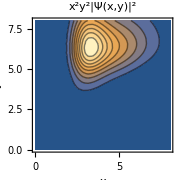

```mathematica
graph2=ContourPlot[Sum[x^(2+2γ⟦k,1⟧)y^(2+2γ⟦k,2⟧)Total[Cij⟦k⟧Exp[-1/2 αij⟦k⟧x^2-1/2 βij⟦k⟧y^2]],{k,γForCalc}],{x,0,8},{y,0,8},PlotRange->Full,AspectRatio->1.,PerformanceGoal->"Quality",ImageSize->Small,FrameLabel->{"x","y"},PlotLabel->"x^2y^2|Ψ(x,y)|^2"]
```

```mathematica
Export[StringJoin[fileName,"_theCP",".jpg"],graph2,"jpg",ImageResolution->1000];
```

```mathematica
graph3=Plot3D[Sum[x^(2+2γ⟦k,1⟧)y^(2+2γ⟦k,2⟧)Total[Cij⟦k⟧Exp[-1/2 αij⟦k⟧x^2-1/2 βij⟦k⟧y^2]],{k,γForCalc}],{x,0,8},{y,0,8},PlotRange->Full,AspectRatio->1.5,PerformanceGoal->"Quality",ImageSize->Small,AxesLabel->{"x, fm","y, fm"},PlotLabel->"x^2y^2|Ψ(x,y)|^2"]
```

-Graphics3D-

```mathematica
Export[StringJoin[fileName,"_the3D",".jpg"],graph3,"jpg",ImageResolution->1000];
```